# Homework 20

## Problem 20.1

Two point masses each of mass m are joined by a spring of spring constant k. The distance between each mass and the center of mass is z. The equilibrium length of the spring is 2z0. The masses slide without friction on a horizontal surface. Both translational and rotational motion are allowed.

For our generalized coordinates, we will use (x,y) as the coordinates of the center of mass, z as the distance between each block and the center of the spring, and theta as the angular coordinate for rotational motion of the masses.

```mathematica
Clear["`*"]
```

Find the Lagrangian of the system. Express it in terms of x, y, z, theta, and their time derivatives xdot, ydot, zdot, thetadot.

```mathematica
T=m*zdot^2+m*(xdot^2+ydot^2)+m*z^2*thetadot^2;
U=k/2*((2*z-2*z0))^2;
L=m*zdot^2+m*(xdot^2+ydot^2)+m*z^2*thetadot^2-k/2*((2*z-2*z0))^2
px=D[2*xdot*m];
py=D[2*ydot*m];
pz=D[2*zdot*m];
ptheta=D[m*z^2*2*thetadot];
```

m (xdot^2+ydot^2)+m thetadot^2 z^2-1/2 k (2 z-2 z0)^2+m zdot^2

### Solutions

```mathematica
T$=m*zdot^2+m*(xdot^2+ydot^2)+m*z^2*thetadot^2;
U$=k/2*((2*z-2*z0))^2;
If[T===T$,Print["T is correct."],Print["T is incorrect."]]
If[U===U$,Print["U is correct."],Print["U is incorrect."]]
If[ptheta===0,Print["You need to include rotational motion of the system."]]
If[T===m/2*zdot^2+m*(xdot^2+ydot^2)+m*z^2*thetadot^2,Print["Remember that both masses have kinetic energy with respect to the center of mass."]]
If[T===m*zdot^2+m/2*(xdot^2+ydot^2)+m*z^2*thetadot^2,Print["Remember that the total mass of the system is 2m rather than m."]]
If[T===m/2*zdot^2+m/2*(xdot^2+ydot^2)+m*z^2*thetadot^2,Print["Remember that the total mass of the system is 2m rather than m and that both masses have kinetic energy with respect to the center of mass."]]
```

T is correct.

U is correct.

Now we wish to write T as an explicit function of px, x, py, y pz, z, ptheta, and theta.  We will do that by solving for the various dot variables and replacing them in the expression for T. 

Then construct H. Is it the same thing you would have constructed intuitively?

```mathematica
sol1=Solve[{px==Px,py==Py,pz==Pz,ptheta==Ptheta},{xdot,ydot,zdot,thetadot}]
T=m*(Pz/2/m)^2+m*((Px/2/m)^2+(Py/2/m)^2)+m*z^2*(Ptheta/2/m/z^2)^2;
H=T+U;
```

{{xdot→Px/(2 m),ydot→Py/(2 m),zdot→Pz/(2 m),thetadot→Ptheta/(2 m z^2)}}

### Solutions

```mathematica
T$=m*(Pz/2/m)^2+m*((Px/2/m)^2+(Py/2/m)^2)+m*z^2*(Ptheta/2/m/z^2)^2;
H$=T$+U;
If[FullSimplify[Solve[T==T$,m]]=={{}},Print["T is correct."],Print["T is incorrect."]]
If[FullSimplify[Solve[H==H$,m]]=={{}},Print["H is correct."],Print["H is incorrect."]]
```

T is correct.

H is correct.

Now take the derivates of H with respect to everything.
Note that most of the equations are pretty simple. Think about what they mean.

```mathematica
dHdx=D[H,x]//Simplify
dHdy=D[H,y]//Simplify
dHdz=D[H,z]//Simplify
dHdtheta:=D[H,theta]//Simplify
dHdPx=D[H,Px]//Simplify
dHdPy=D[H,Py]//Simplify
dHdPz=D[H,Pz]//Simplify
dHdPtheta=D[H,Ptheta]//Simplify
```

0

0

-Ptheta^2/(2 m z^3)+4 k (z-z0)

Px/(2 m)

Py/(2 m)

Pz/(2 m)

Ptheta/(2 m z^2)

Construct the equations of motion, being sure to include the explicit time dependence of each variable (e.g. Px[ t ]).

```mathematica
eq1=0==-Px'[t]
eq2=0==-Py'[t]
eq3=-1/2/m/z[t]^3*Ptheta[t]^2+2*k*(2*z[t]-2*z0)==-Pz'[t]
eq4=0==-Ptheta'[t]
eq5=Px[t]/2/m==x'[t]
eq6=Py[t]/2/m==y'[t]
eq7=Pz[t]/2/m==z'[t]
eq8=1/2*Ptheta[t]/m/z[t]^2==theta'[t]
```

0==-Px'[t]

0==-Py'[t]

-Ptheta[t]^2/(2 m z[t]^3)+2 k (-2 z0+2 z[t])==-Pz'[t]

0==-Ptheta'[t]

Px[t]/(2 m)==x'[t]

Py[t]/(2 m)==y'[t]

Pz[t]/(2 m)==z'[t]

Ptheta[t]/(2 m z[t]^2)==theta'[t]

### Solutions

```mathematica
eq1$=0==-Px'[t];
eq2$=0==-Py'[t];
eq3$=-1/2/m/z[t]^3*Ptheta[t]^2+2*k*(2*z[t]-2*z0)==-Pz'[t];
eq4$=0==-Ptheta'[t];
eq5$=Px[t]/2/m==x'[t];
eq6$=Py[t]/2/m==y'[t];
eq7$=Pz[t]/2/m==z'[t];
eq8$=1/2*Ptheta[t]/m/z[t]^2==theta'[t];
If[eq1===eq1$,Print["eq1 is correct"],Print["eq1 is incorrect"]]
If[eq2===eq2$,Print["eq2 is correct"],Print["eq2 is incorrect"]]
If[Simplify[eq3]===Simplify[eq3$],Print["eq3 is correct"],Print["eq3 is incorrect"]]
If[eq4===eq4$,Print["eq4 is correct"],Print["eq4 is incorrect"]]
If[eq5===eq5$,Print["eq5 is correct"],Print["eq5 is incorrect"]]
If[eq6===eq6$,Print["eq6 is correct"],Print["eq6 is incorrect"]]
If[eq7===eq7$,Print["eq7 is correct"],Print["eq7 is incorrect"]]
If[Simplify[eq8]===Simplify[eq8$],Print["eq8 is correct"],Print["eq8 is incorrect"]]
```

eq1 is correct

eq2 is correct

eq3 is correct

eq4 is correct

eq5 is correct

eq6 is correct

eq7 is correct

eq8 is correct

```mathematica
m=1;
z0=0.2;
k=6;
L0=12;
d=.4;
```

Now turn it into a differential equation and solve numerically.

```mathematica
sol=NDSolve[{eq3,eq4,eq7,eq8,z[0]==d/2,Pz[0]==0,theta[0]==0,Ptheta[0]==L0},{z,Pz,theta,Ptheta},{t,0,3}]
```

{{z→InterpolatingFunction[…],Pz→InterpolatingFunction[…],theta→InterpolatingFunction[…],Ptheta→InterpolatingFunction[…]}}

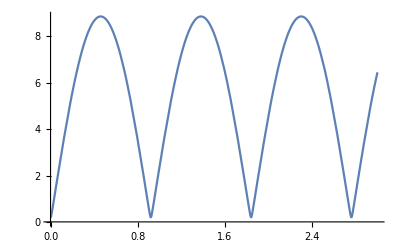

```mathematica
Plot[Evaluate[z[t]/.sol],{t,0,3}]
```

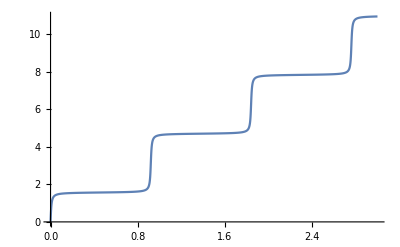

```mathematica
Plot[Evaluate[theta[t]/.sol],{t,0,3}]
```

Can you explain why the system behaves this way?

## Problem 20.2

This is the example from class, but you'll rework it with different coordinates. A mass m1 is connected by a spring to a wall. A mass m2 is connected to mass m1 by an identical spring. We let x1 be the distance of m1 from the wall, and x2 be the distance of m2 from the wall. The springs are identical with spring constant is k and the equilibrium length of the spring is x0.

Compress each spring to a length x0/2 and then release them from rest. Plot x1[ t ], x2[t], and x2[ t ]-x1[ t ].
m1 = 0.250
m2 = 0.125
x0 = 0.3
k = 1.24

(You may ignore the length of each mass.)

```mathematica
Quit[]
Clear["`*"]
```

## Part A

Write the Hamiltonian as a function of x1, p1, x2, and p2. Note that the kinetic energy is very simple with this choice of coordinates! -- The potential energy is just a little tricky, however.

```mathematica
T=p1^2/2/m1+p2^2/2/m2;
U=k*(x1-x0)^2/2+k*(x2-x1-x0)^2/2;
H=T$+U$;
```

### Solutions

```mathematica
T$=p1^2/2/m1+p2^2/2/m2;
U$=k*(x1-x0)^2/2+k*(x2-x1-x0)^2/2;
H$=T$+U$;
If[T===T$,Print["T is correct."],Print["T is incorrect."]]
If[U===U$,Print["U is correct."],Print["U is incorrect."]]
If[H===H$,Print["H is correct."],Print["H is incorrect."]]
```

T is correct.

U is correct.

H is correct.

Find the derivatives of the Hamiltonian.

```mathematica
dHdx1=D[H,x1]//Simplify
dHdx2=D[H,x2]//Simplify
dHdp1=D[H,p1]//Simplify
dHdp2=D[H,p2]//Simplify
```

k (2 x1-x2)

-k (x0+x1-x2)

p1/m1

p2/m2

Now write the equations of motion explicitly showing the time dependence of the variables.

```mathematica
eq1=k*(x1[t]-x0)-k*(x2[t]-x1[t]-x0)==-p1'[t]
eq2=k*(x2[t]-x1[t]-x0)==-p2'[t]
eq3=1/m1*p1[t]==x1'[t]
eq4=1/m2*p2[t]==x2'[t]
```

k (-x0+x1[t])-k (-x0-x1[t]+x2[t])==-p1'[t]

k (-x0-x1[t]+x2[t])==-p2'[t]

p1[t]/m1==x1'[t]

p2[t]/m2==x2'[t]

### Solutions

```mathematica
eq1$=k*(x1[t]-x0)-k*(x2[t]-x1[t]-x0)==-p1'[t];
eq2$=k*(x2[t]-x1[t]-x0)==-p2'[t];
eq3$=1/m1*p1[t]==x1'[t];
eq4$=1/m2*p2[t]==x2'[t];
If[eq1===eq1$,Print["eq1 is correct"],Print["eq1 is incorrect"]]
If[eq2===eq2$,Print["eq2 is correct"],Print["eq2 is incorrect"]]
If[eq3===eq3$,Print["eq3 is correct"],Print["eq3 is incorrect"]]
If[eq4===eq4$,Print["eq4 is correct"],Print["eq4 is incorrect"]]
```

eq1 is correct

eq2 is correct

eq3 is correct

eq4 is correct

Now solve the differential equations:

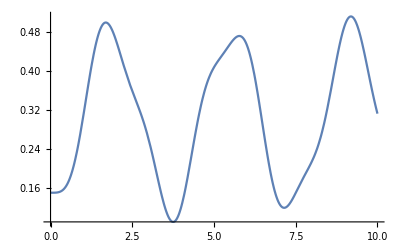

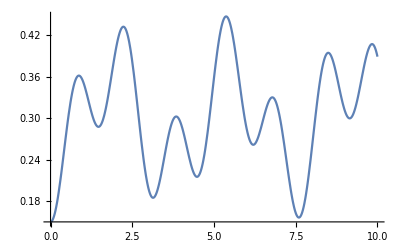

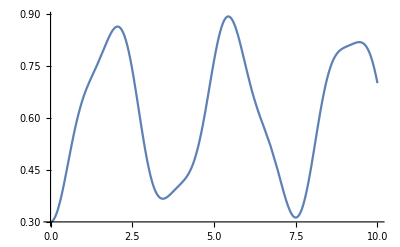

```mathematica
m1=.250;
m2=.125;
x0=0.3;
k=1.24;
sol=NDSolve[{eq1,eq2,eq3,eq4,x1[0]==x0/2,p1[0]==0,x2[0]==x0,p2[0]==0},{x1[t],x2[t],p1[t],p2[t]},{t,0,10}];
Plot[Evaluate[x1[t]/.sol],{t,0,10}]
Plot[Evaluate[(x2[t]-x1[t])/.sol],{t,0,10}]
Plot[Evaluate[x2[t]/.sol],{t,0,10}]
```

## Written Problems

-Graphics-

```mathematica
Clear["`*"]
```

```mathematica
Simplify[1/2*k*((a^2+b^2-2*b*y+y^2)/L)^2]
```

(k (a^2+(b-y)^2)^2)/(2 L^2)

```mathematica
Distribute[(a^2+b^2-2*b*y+y^2)^2]
```

a^4+b^4+4 b^2 y^2+y^4